```mathematica
PredicateName[p_Symbol]:= p (* Special case usable for simpler representation of propositional logic *)
PredicateName[p_[x___]]:=p
PredicateSymbols[Not[a_]] := PredicateSymbols[a]
PredicateSymbols[a_∧b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_∨b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_⊻b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_⇒b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[a_⧦b_]:= PredicateSymbols[a]∪PredicateSymbols[b]
PredicateSymbols[p_Symbol[x_]]:= {{p, 1}}
PredicateSymbols[p_Symbol[x_,y_]]:={{p,2}}
BinaryPredicateSymbols[ϕ_]:=First /@Select[PredicateSymbols[ϕ],#[[2]]==2&]
UnaryPredicateSymbols[ϕ_]:=First /@Select[PredicateSymbols[ϕ],#[[2]]==1&]
BinaryNonreflexiveAtoms[ϕ_]:=Flatten[{#[a,b],#[b,a]}&/@ BinaryPredicateSymbols[ϕ]]
PredicateToAtom[{p_,1}]:=p[a]
PredicateToAtom[{p_,2}]:=p[a,a]
UnaryAndReflexiveAtoms[ϕ_]:= PredicateToAtom/@ PredicateSymbols[ϕ]
FOAtoms[False] := {}
FOAtoms[True] := {}
FOAtoms[Not[ϕ_]] := FOAtoms[ϕ]
FOAtoms[ϕ_∧ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_∨ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[ϕ_⇒ψ_]:= FOAtoms[ϕ]∪FOAtoms[ψ]
FOAtoms[atom_]:= {atom}
PositiveAtoms[model_List]:=model/.{(a_->False) :> Nothing, (a_->True) :> a}
NegativeAtoms[model_List]:=model/.{(a_->True) :> Nothing, (a_->False) :> a}
PredicateSymbol[p_Symbol[x___]]:= {p, Length[x]}
PredicateSymbols[ϕ_]:= PredicateSymbol/@ FOAtoms[ϕ]
MakeLiteral[a_->True]:= a
MakeLiteral[b_->False]:= ¬b
InterpretationToFormula[f_List]:= And@@(MakeLiteral /@ f)
SymbolSetWeight[set_List, weights_]:= Times@@ (weights /@set)
GroundAtomSetWeight[set_List, weights_]:=SymbolSetWeight[PredicateName/@ set, weights]
ModelWeight[model_, weightsPositive_, weightsNegative_]:= (* FIXME - this should be easy to make 2x faster *)
GroundAtomSetWeight[PositiveAtoms[model], weightsPositive] * GroundAtomSetWeight[NegativeAtoms[model], weightsNegative]
AllModels[False]:= {};
AllModels[ϕ_,variables_]:=Module[{result},
(modelBool↦Thread[variables->modelBool])/@
SatisfiabilityInstances[ϕ,variables,All]
(*Print[result];
result*)
]
WeightedModels[ϕ_,weightsPositive_, weightsNegative_, variables_]:=Total[ (*naive WMC implementation using SAT *)
(model ↦ModelWeight[model, weightsPositive, weightsNegative])/@
AllModels[ϕ,variables]
]
PredicateToAtom[{p_,1}]:= p[a]
PredicateToAtom[{p_,2}]:= p[a,a]
CellAtoms[predicates_List]:=PredicateToAtom/@ predicates
(*MakeCell[atoms_List,fs_List]:=  And@@MapThread[#1[#2]&,{fs,atoms}] *)(* just a helper function for AllCells *)
MakeCell[atoms_List,boolVec_List]:= Thread[atoms->boolVec]
AllCells[atoms_List]:=
(boolVec ↦MakeCell[atoms,boolVec])/@
Tuples[{False,True}, Length[atoms]]
FormulaCells[ϕ_]:= Sort@AllCells@CellAtoms@PredicateSymbols[ϕ] (* Sort probably not needed - added just in case to ensure function purity *)
FormulaCellsValid[ϕ_]:=Module[
{cells=FormulaCells[ϕ]},
Pick[cells,SatisfiableQ[(ϕ/. b->a)/.#]& /@ cells]
]
SwapVariables[object_]:= object /. {a->b, b->a}
FormulaSymmetric[ψ_]:=ψ∧SwapVariables[ψ]
FormulaReflexive[ψ_]:= ψ /. b->a
FormulaSimplified[ψ_, cell1_, cell2_]:=FormulaSymmetric[ψ] /.Join[cell1, SwapVariables[cell2]]
FormulaSimplified[ψ_,cell_]:=FormulaSimplified[ψ, cell, cell]
RTerm[{ψ_,weightsPositive_, weightsNegative_},cell1_,cell2_]:=Module[
{unaryWeights = (#->1)&/@ UnaryPredicateSymbols[ψ]}, (* Podle Timova kódu - nechápu proč *)
WeightedModels[
(*Alternative : syntactic approach to cells:
Simplify[FormulaSymmetric[ψ]∧ InterpretationToFormula[cell1]∧InterpretationToFormula@SwapVariables[cell2]],
Semantic:
FormulaSimplified2Cell[ψ, cell1, cell2],
*)
FormulaSimplified[ψ, cell1, cell2],
Association[weightsPositive,unaryWeights],
Association[weightsNegative,unaryWeights],
BinaryNonreflexiveAtoms[ψ]
]
]
STerm[{ψ_,weightsPositive_, weightsNegative_},cell_]:=RTerm[{ψ, weightsPositive, weightsNegative}, cell, cell]
WTerm[{ψ_,weightsPositive_, weightsNegative_},cell_]:=
WeightedModels[
FormulaReflexive[ψ]∧ InterpretationToFormula[cell],
weightsPositive, weightsNegative,
UnaryAndReflexiveAtoms[ψ]
]
STerms[{ψ_, weightsPositive_, weightsNegative_}]:= (cell↦STerm[{ψ, weightsPositive, weightsNegative}, cell]) /@ FormulaCellsValid[ψ]
WTerms[{ψ_, weightsPositive_, weightsNegative_}]:= (cell↦WTerm[{ψ, weightsPositive, weightsNegative}, cell]) /@ FormulaCellsValid[ψ]
RTerms[{ψ_, weightsPositive_, weightsNegative_}] := Module[
{
cells = FormulaCellsValid[ψ],
length
},
length = Length[cells];
(row ↦PadRight[row, length]) /@
Table[
RTerm[{ψ, weightsPositive,weightsNegative},cells⟦i⟧, cells⟦j⟧],
{i, 1, length},{j, 1, i-1}
]
]
RTermsFull[{ψ_, weightsPositive_, weightsNegative_}] := Module[
{cells = FormulaCellsValid[ψ], length},
length = Length[cells];
(row ↦PadRight[row, length]) /@
Table[
RTerm[{ψ, weightsPositive,weightsNegative},cells⟦i⟧, cells⟦j⟧],
{i, 1, length},{j, 1, length}
]
]
SWR[property_] := {STerms[property],WTerms[property],RTerms[property] }
SRMat[s_,r_]:=DiagonalMatrix[s]+r+Transpose[r]
CompatibilityCondition1[i_Integer,cliquePart_List,s_]:=AllTrue[cliquePart,j↦s⟦i⟧===s⟦j⟧]
CompatibilityCondition2[i_Integer,cliquePart_List,w_]:=AllTrue[cliquePart,j↦w⟦i⟧===w⟦j⟧]
CompatibilityCondition3[i_Integer,cliquePart_List,r_]:=AllTrue[
Tuples[{cliquePart,Complement[Range@Length[r], cliquePart]}],
Replace[#,{j_,k_}:> (j<k∧ i!= j)⇒ (r⟦i,k⟧===r⟦j,k⟧)]&
]
CompatibilityCondition4[i_Integer,cliquePart_List,r_]:=AllTrue[
Tuples[{cliquePart,cliquePart, cliquePart}],
 Replace[#,{j_,k_,l_}:> (i<j∧k<l)⇒ (r⟦i,j⟧===r⟦k,l⟧)]&
]
(*Compatible[i_Integer, cliquePart_List, {s_,w_,r_}]:=Module[{ 
all=Range@Length[s],
cond3= {j_,k_}:> (j<k∧ i!= j)⇒ (r⟦i,k⟧===r⟦j,k⟧),
cond4= {j_,k_,l_}:> (i<j∧k<l)⇒ r⟦i,j⟧===r⟦k,l⟧
},
And[
AllTrue[cliquePart,j↦s⟦i⟧===s⟦j⟧],
AllTrue[cliquePart,j↦w⟦i⟧===w⟦j⟧],
And@@Tuples[{cliquePart,Complement[all, cliquePart]}]/.cond3,
And@@Tuples[{cliquePart, cliquePart, cliquePart}]/.cond4
]
]*)
SRratio[s_,r_, {c1_,c2_, rest___}]:=
s[[c1]]/r[[c2,c1]]
Compatible[i_Integer, cliquePart_List, {s_,w_,r_}]:=
CompatibilityCondition1[i,cliquePart,s]∧ 
CompatibilityCondition2[i,cliquePart,w]∧
CompatibilityCondition3[i,cliquePart,r]∧
CompatibilityCondition4[i,cliquePart,r]
Cliques[{s_,w_,r_}]:=Module[
{i, j, cliques={}, length = Length[s],current, all},
all = Range[length];
While[Length[all]>0,
current = {};
(cell↦ If[
Compatible[cell, current, {s,w,r}] ,
AppendTo[current, cell];
all = all /. cell -> Nothing;
]
) /@ all;
AppendTo[cliques, current]
];
cliques
]
(*
GetGTerm[0, n_Integer,cliqueIds_List]:= GetGTerm[0, n,cliqueIds] = Module[
(i↦ ) /@ Range[1,k]
]
GetGTerm[p_Integer, n_Integer,cliqueIds_List]:= GetGTerm[p, n,cliqueIds] = Module[
{s=0},
]*)
(* TODO - memoization *)
```

```mathematica
exampleDerangements= {
¬f[a,a] ∧ (f[a,b]⇒s1[a])∧(f[b,a]⇒s2[a]),
<|f->z,s1->1,s2->1|>,
<|f->1,s1->-1,s2->-1|>};
examplePermutations= {
(f[a,b]⇒s1[a])∧(f[b,a]⇒s2[a]),
<|f->z,s1->1,s2->1|>,
<|f->1,s1->-1,s2->-1|>};
exampleFunctions = {
f[a,b]⇒s1[a],
<|f->z,s1->1|>,
<|f->1,s1->-1|>};
exampleInvolutions = {
(f[a,b]⇒s1[a])∧(f[a,b]⇒f[b,a]),
<|f->z,s1->1|>,
<|f->1,s1->-1|>};
example1Regularity = {
¬f[a,a] ∧ (f[a,b]⇒s1[a])∧(f[b,a]⇒s2[a])∧(f[a,b]⇒f[b,a]),
<|f->z,s1->1,s2->1|>,
<|f->1,s1->-1,s2->-1|>};
example2Regularity = {
¬e[a,a]∧
 (e[a,b]⧦e[b,a])∧
(f1[a,b]⇒s1[a])∧
(f2[a,b]⇒s2[a])∧
(e[a,b]⧦(f1[a,b]∨f2[a,b]))∧ 
(¬f1[a,b]∨¬f2[a,b]),
<|e->z,s1->1,s2->1,f1->1,f2->1|>,
<|e->1,s1->-1,s2->-1,f1->1,f2->1|>
};
example3Regularity= {
¬e[a,a]∧
 (e[a,b]⇒e[b,a])∧
(f1[a,b]⇒s1[a])∧
(f2[a,b]⇒s2[a])∧
(f3[a,b]⇒s3[a])∧
(e[a,b]⧦(f1[a,b]∨f2[a,b]∨f3[a,b]))∧
(¬f1[a,b]∨¬f2[a,b])∧
(¬f1[a,b]∨¬f3[a,b])∧
(¬f2[a,b]∨¬f3[a,b]),
<|e->z,s1->1,s2->1,s3->1,f1->1,f2->1,f3->1|>,
<|e->1,s1->-1,s2->-1,s3->-1,f1->1,f2->1,f3->1|>
};
example3Coloredness={
¬e[a,a]∧
(e[a,b]⇒e[b,a])∧
(c1[a]∨c2[a]∨c3[a])∧
(¬c1[a]∨ ¬c2[a])∧
(¬c3[a]∨ ¬c2[a])∧
(¬c1[a]∨ ¬c3[a])∧
(e[a,b]⇒ (¬(c1[a]∧c1[b])∧¬(c2[a]∧c2[b])∧¬(c3[a]∧c3[b]))),
<|e->1,c1->1,c2->1,c3->1|>,
<|e->1,c1->1,c2->1,c3->1|>
};
example2Coloredness={
¬e[a,a]∧
(e[a,b]⇒e[b,a])∧
(c1[a]⊻ c2[a])∧
(e[a,b]⇒ (¬(c1[a]∧c1[b])∧¬(c2[a]∧c2[b]))),
<|e->1,c1->1,c2->1|>,
<|e->1,c1->1,c2->1|>
};
{sder,wder,rder}=SWR[exampleDerangements];
{sfunc,wfunc,rfunc} =SWR[exampleFunctions];
{sinvol,winvol,rinvol} =SWR[exampleFunctions];
{s1reg,w1reg,r1reg} = SWR[example1Regularity];
{s2reg,w2reg,r2reg} = SWR[example2Regularity];
{s2col,w2col,r2col} = SWR[example2Coloredness];
{s3col,w3col,r3col} = SWR[example3Coloredness];
example = example2Regularity;
{s,w,r}=SWR[example];
rfull=RTermsFull[exampleDerangements]; MatrixForm[r]
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 1+z^2 | 0 | 0
1 | 1+2 z^2 | 1+2 z^2 | 0)

{{{f[a,a]→False,s1[a]→False,s2[a]→False},{f[a,a]→False,s1[a]→False,s2[a]→True}},{{{f[a,a]→False,s1[a]→True,s2[a]→True}}}}

{{1},{2,3},{4}}

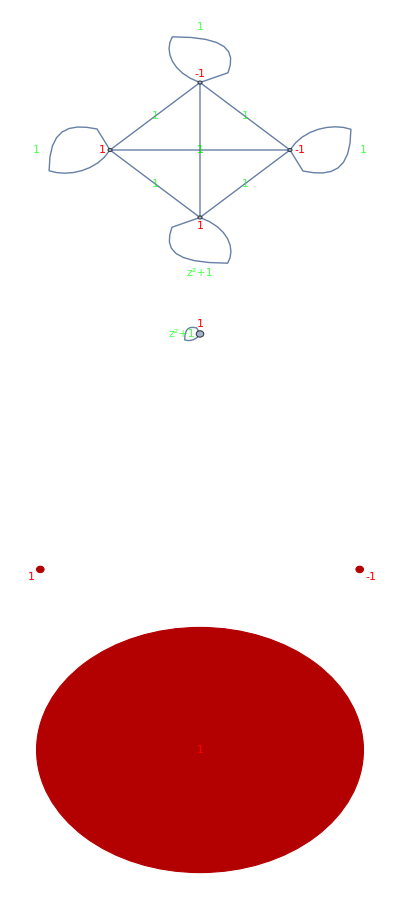

{{{f[a,a]→False,s1[a]→False,s2[a]→False},{f[a,a]→False,s1[a]→False,s2[a]→True}},{{{f[a,a]→False,s1[a]→True,s2[a]→True}}}}

```mathematica
CellGraphEdges[cells_] := Flatten[Table[cells⟦i⟧<-> cells⟦j⟧, {j, 1, Length[cells]},{i,1,j}],2]
CellGraph[specification_]:= Module[
{
cells =FormulaCellsValid[First[specification]],
edgeLabeling = (cell1_<->cell2_):> (
(cell1<->cell2) ->
RTerm[specification, cell1,cell2]), (* Note: This automagically coumputes S-terms at loops *)
vertexLabeling=cell↦(
cell ->WTerm[specification, cell])
},
With[
{edges= CellGraphEdges[cells]},
Graph[
edges,
EdgeWeight-> edges /. edgeLabeling,
EdgeLabels->"EdgeWeight",
VertexLabels->(vertexLabeling) /@ cells,
GraphLayout->"CircularEmbedding",
EdgeLabelStyle->Green,
VertexLabelStyle->Red,
ImageSize->Medium
]
]
]
LoopQ[a_->b_]:=a==b
LoopQ[a_<->b_]:=a==b
LoopList[g_]:= Select[EdgeList[g], LoopQ]
LoopyVertexDelete[g_]:=VertexDelete[g, First/@ LoopList[g]]
FindIndependentVertexSetNoloop[g_]:=
If[EmptyGraphQ[g],
{},
First@FindIndependentVertexSet@LoopyVertexDelete[g]
]
EdgeWeights[g_]:=Thread[{EdgeList[g],AnnotationValue[g,EdgeWeight]}]
CellGraphCollapsed[specification_]:=Module[
{g=CellGraph[specification], cliques = Cliques@SWR[specification],cells},
cells=VertexList[g];
VertexDelete[g,
cells[[#]]&/@Flatten[Rest/@ cliques]]
]
CellGraphIndependent[specification_]:=Module[
{g=CellGraphCollapsed[specification]},
EdgeDelete[g,
First/@Select[
EdgeWeights[g],
Last[#]==1&
]
]
]
CellGraphIndependentReduced[cellGraphIndependent_, i1_]:=
VertexDelete[
EdgeDelete[cellGraphIndependent, LoopList[cellGraphIndependent]],
VertexList@NeighborhoodGraph[cellGraphIndependent,i1]
]
IndependetSets[specification_]:= Module[
{cellGraphIndependent=CellGraphIndependent[specification],cellGraphIndependentReduced,i1,i2},
i1 = FindIndependentVertexSetNoloop[cellGraphIndependent];
cellGraphIndependentReduced=CellGraphIndependentReduced[cellGraphIndependent,i1];
i2= FindIndependentVertexSet[cellGraphIndependentReduced]; (* Naturally loopless *)
{i1,i2}
]


example=example1Regularity;
{i1,i2}=IndependetSets[example]
cellGraph = CellGraph[example];
cellGraphIndependent = CellGraphIndependent[example];
cellGraphIndependentReduced=CellGraphIndependentReduced[cellGraphIndependent,i1];
cliques=Cliques[SWR[example] ]
Column[{cellGraph,HighlightGraph[cellGraphIndependent,i1],HighlightGraph[cellGraphIndependentReduced,i2]}]
IndependetSets[example]
```

```mathematica
PolyToEGF[poly_,var_]:= Module[
{coefs=CoefficientList[poly,var]},
Sum[(coefs[[i+1]] *var^i)/(i!),{i,0,Length[coefs]-1}]
]
```

```mathematica
(* Implementation of WFOMC according to formula (1) in Faster Lifting for Two-Variable Logic using Cell Graphs *)
OrderedPartitions[n_Integer,m_Integer]:= Flatten[
Permutations[PadRight[#,m]]&
/@IntegerPartitions[n,m],
1]
OrderedPartitionsUpTo[n_Integer,m_Integer]:= 
Catenate@Table[OrderedPartitions[i,m],{i,0,n}]
Pow[0,0]:=1
Pow[a_,b_]:=a^b
GetDTerm[k_,n_, srratio_] := GetDTerm[1, k,n] 
GetDTerm[i_, k_,n_,srratio_] := 
If[i==k,
srratio^Binomial[n,2],
Sum[
Binomial[n,ni]*srratio^Binomial[ni,2]*GetDTerm[i+1, k,n-ni,srratio],
{ni,0,n}]
]
GetJTerm[{cell_},n_, s_,r_]:=s[[cell]]^Binomial[n,2]
GetJTerm[clique_List,n_, s_,r_] :=
Module[
{
srratio=SRratio[s,r,clique],
k=Length[clique]
},
r[[clique[[2]],clique[[1]]]]^Binomial[n,2] * GetDTerm[k,n,srratio]
]
GetGTerm[0,n_,partition_, N_, k_,l_, {s_,w_,r_}]:=
Sum[w[[i]]*Product[r[[i,j]] ~Pow~ partition[[j-k-l]],{j,k+l+1,Length[r]}],{i,1,k}]~Pow~(n-N-Total[partition])
GetGTerm[p_,n_,partition_, N_, k_,l_, {s_,w_,r_}]:=Module[
{ub=n-N-Total[partition]},
Sum[
Binomial[ub,nkp]*(w[[k+p]]~Pow~nkp)*GetJTerm[{k+p},nkp,s,r]*Product[r[[k+p,j]]~Pow~(nkp*partition[[j-k-l]]),{j,k+l+1,Length[r]}]*GetGTerm[p-1, n,partition,N+nkp, k,l,{s,w,r}],
{nkp,0,ub}
]
]
WFOMC1[n_Integer,property_]:= Module[{
s,w,r,u,i,j
},
{s,w,r}=SWR[property];
u=Length[s];
Total[(partition |-> 
Multinomial[Sequence@@partition] *
Product[
r⟦i,j⟧~Pow~(partition⟦i⟧*partition⟦j⟧),
{i,1,u},
{j,1 , i-1}]*
Product[
s⟦i⟧~Pow~Binomial[partition⟦i⟧,2] *
 w⟦i⟧~Pow~partition⟦i⟧,
{i,1,u}]
) /@ OrderedPartitions[n, u]]
]
FastWFOMC[n_Integer, property_]:=Module[{
s,w,r,k , l,ncliques
}, 
{s,w,r}=SWR[property];
ncliques=Length@Cliques[{s,w,r}];
{k,l}=Length/@IndependetSets[property];
{k,l}={1,1};
Total[(partition|-> 
Multinomial[Sequence@@partition]*
Product[
Evaluate[r⟦i,j⟧]~Pow~Evaluate[partition⟦i⟧*partition⟦j⟧],
{i,k+l+1,ncliques},
{j,k+l+1 , i-1}]*
Product[
 (w⟦i⟧~Pow~partition⟦i⟧)*GetJTerm[{partition[[i]]},n,s,r],
{i,k+l+1,ncliques}]*
GetGTerm[l,n,partition,0,k,l,{s,w,r}]
)/@ (PadLeft[#,ncliques]&/@OrderedPartitionsUpTo[n, ncliques-k-l-1])
]
]
```

```mathematica
maxN=6;
wfomc=Table[
WFOMC1[n,exampleDerangements],
 {n, 0, maxN}];
Simplify[wfomc]
wfomcCc = Table[Coefficient[wfomc[[n+1]],z,n], {n,0,maxN}]
%/ (6^Range[0,maxN])
```

{1,0,z^2,z^3 (2+9 z+6 z^2+z^3),z^4 (9+108 z+352 z^2+516 z^3+423 z^4+212 z^5+66 z^6+12 z^7+z^8),z^5 (44+1170 z+8780 z^2+32335 z^3+72720 z^4+111986 z^5+126140 z^6+108055 z^7+71940 z^8+37560 z^9+15344 z^10+4835 z^11+1140 z^12+190 z^13+20 z^14+z^15),z^6 (265+12780 z+176820 z^2+1223530 z^3+5284221 z^4+16017720 z^5+36583930 z^6+65929770 z^7+96728325 z^8+118061144 z^9+121689765 z^10+107001420 z^11+80771565 z^12+52509120 z^13+29408121 z^14+14155380 z^15+5825325 z^16+2032200 z^17+593475 z^18+142494 z^19+27405 z^20+4060 z^21+435 z^22+30 z^23+z^24)}

{1,0,1,2,9,44,265}

{1,0,1/36,1/108,1/144,11/1944,265/46656}

```mathematica
maxN=6;
wfomc=Table[
FastWFOMC[n,exampleDerangements],
 {n, 0, maxN}];
Simplify[wfomc]
wfomcCc = Table[Coefficient[wfomc[[n+1]],z,n], {n,0,maxN}]
%/ (6^Range[0,maxN])
```

{1,0,0,0,0,0,0}

{1,0,0,0,0,0,0}

{1,0,0,0,0,0,0}

```mathematica
FormulaCellsValid[example2Regularity[[1]]]
SatisfiabilityInstances[
example2Regularity[[1]]/.#,
{e[a,b],e[b,a],f1[a,b],f2[a,b]}
]& /@  % // Column
```

{{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→False,s2[a]→False},{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→False,s2[a]→True},{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→True,s2[a]→False},{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→True,s2[a]→True}}

{{False,False,False,False}}
{{True,True,False,True}}
{{True,True,True,False}}
{{True,True,True,False}}

```mathematica
FormulaCellsValid[example2Regularity[[1]]] // Column
```

{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→False,s2[a]→False}
{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→False,s2[a]→True}
{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→True,s2[a]→False}
{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→True,s2[a]→True}

```mathematica
SatisfiabilityInstances[(¬e∨ f1∨ f2)∧(f1⇒e)∧(f2⇒e),{e,f1,f2},All]
SatisfiabilityInstances[e⧦(f1∨f2),{e,f1,f2},All]
```

{{True,True,True},{True,True,False},{True,False,True},{False,False,False}}

{{True,True,True},{True,True,False},{True,False,True},{False,False,False}}

```mathematica
#->1&/@ UnaryPredicateSymbols[First@example2Regularity]
```

{s1→1,s2→1}

```mathematica
STerm[example2Regularity[[1]],{e[a,a]->False,f1[a,a]->False,f2[a,a]->False,s1[a]->False,s2[a]->False},example2Regularity[[2]], example2Regularity[[3]]]
```

STerm[!e[a,a]&&(e[a,b]⧦e[b,a])&&(f1[a,b]⇒s1[a])&&(f2[a,b]⇒s2[a])&&(e[a,b]⧦f1[a,b]||f2[a,b])&&(!f1[a,b]||!f2[a,b]),{e[a,a]→False,f1[a,a]→False,f2[a,a]→False,s1[a]→False,s2[a]→False},<|e→z,s1→1,s2→1,f1→1,f2→1|>,<|e→1,s1→-1,s2→-1,f1→1,f2→1|>]

```mathematica
example2Regularity[[1]] /. {e[a,a]->False,f1[a,a]->False,f2[a,a]->False,s1[a]->False,s2[a]->False}
FormulaSymmetric[example2Regularity[[1]]] /. {e[a,a]->False,f1[a,a]->False,f2[a,a]->False,s1[a]->False,s2[a]->False} /. ( {e[a,a]->False,f1[a,a]->False,f2[a,a]->False,s1[a]->False,s2[a]->False} /.a->b)
```

(e[a,b]⧦e[b,a])&&!f1[a,b]&&!f2[a,b]&&(e[a,b]⧦f1[a,b]||f2[a,b])&&(!f1[a,b]||!f2[a,b])

(e[a,b]⧦e[b,a])&&!f1[a,b]&&!f2[a,b]&&(e[a,b]⧦f1[a,b]||f2[a,b])&&(!f1[a,b]||!f2[a,b])&&(e[a,b]⧦e[b,a])&&!f1[b,a]&&!f2[b,a]&&(e[b,a]⧦f1[b,a]||f2[b,a])&&(!f1[b,a]||!f2[b,a])

```mathematica
s2reg // MatrixForm
```

(1
1+z^2
1+z^2
1+4 z^2)

```mathematica
Solve[1+4 z^2==0,z]
```

{{z→-ⅈ/2},{z→ⅈ/2}}

```mathematica
s[[cliques[[3]]]]
```

{1+4 z^2}

```mathematica
#[[cliques[[2]]]]&/@(r+Transpose[r])[[cliques[[2]]]]
```

{{0,1+z^2},{1+z^2,0}}

```mathematica
cliques
```

{{1},{2,3},{4}}

```mathematica
r[[2,3]]
r[[3,2]]
```

0

1+z^2

```mathematica
cliques
```

{{1},{2,3},{4}}

```mathematica
SRratio[s,r,cliques[[2]]]
```

1

```mathematica
SRMat[s,r]//MatrixForm
```

(1 | 1 | 1 | 1
1 | 1+z^2 | 1+z^2 | 1+2 z^2
1 | 1+z^2 | 1+z^2 | 1+2 z^2
1 | 1+2 z^2 | 1+2 z^2 | 1+4 z^2)

```mathematica
LinearSolve[SRMat[s,r],w]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1,1,1},{1,1+z^2,1+z^2,1+2 z^2},{1,1+z^2,1+z^2,1+2 z^2},{1,1+2 z^2,1+2 z^2,1+4 z^2}},{1,-1,-1,1}]

{{1,1+2 z+z^2,1+2 z+z^2},{-1,1,z},{{0,0,0},{1+z,0,0},{1+z,1+2 z+z^2,0}}}

(-1 | 0 | 0
((1+z) (1+ⅇ^(ⅈ (1+z)^2 π)))/(z (2+z)) | ⅇ^(ⅈ (1+z)^2 π) | 0
-((1+z) (1+ⅇ^(ⅈ (1+z)^2 π)))/(z^2 (2+z)^2)+(ⅈ (1+z)^3 ⅇ^(ⅈ (1+z)^2 π) π)/(z (2+z)) | ⅈ (1+z)^2 ⅇ^(ⅈ (1+z)^2 π) π | ⅇ^(ⅈ (1+z)^2 π))

{1+((1+z) ⅇ^(-ⅈ (1+z)^2 π) (1+ⅇ^(ⅈ (1+z)^2 π)))/(z (2+z))-((1+z) ⅇ^(-ⅈ (1+z)^2 π) (ⅇ^(ⅈ (1+z)^2 π)+ⅈ (-ⅈ+2 z π+5 z^2 π+4 z^3 π+z^4 π)))/(z (2+z)^2),ⅇ^(-ⅈ (1+z)^2 π)-ⅈ z (1+z)^2 ⅇ^(-ⅈ (1+z)^2 π) π,z ⅇ^(-ⅈ (1+z)^2 π)}

ⅇ^(-2 ⅈ π (1+z)^2) z^2-ⅇ^(-2 ⅈ π (1+z)^2) (ⅈ+π z+2 π z^2+π z^3)^2+(1+(ⅇ^(-ⅈ π (1+z)^2) (1+ⅇ^(ⅈ π (1+z)^2)) (1+z))/(z (2+z))-(ⅇ^(-ⅈ π (1+z)^2) (1+z) (ⅇ^(ⅈ π (1+z)^2)+ⅈ (-ⅈ+2 π z+5 π z^2+4 π z^3+π z^4)))/(z (2+z)^2))^2

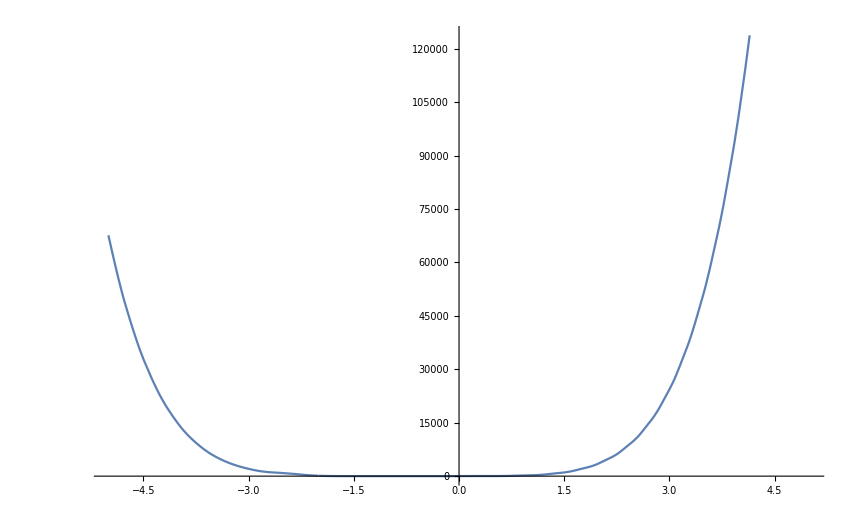

```mathematica
SRMat2[s_,r_]:=MatrixExp[ ⅈ π(DiagonalMatrix[s ]+r)]
{s,w,r}=SWR[exampleFunctions]
srmat=SRMat2[s,r];
MatrixForm[srmat]
pinv = Simplify@PseudoInverse[srmat];
MatrixForm[pinv];
sol=w.pinv 
norm2=Simplify[sol.sol] /.z->z
Plot[Abs[norm2],{z,-5,5}]
```